```mathematica
(*denomnator 231012&14note*)
(*k1*)
Simplify[√-ⅈ==(1-ⅈ)/(√2)]
```

True

cot(k1 L)の変形（分母の2項目d2の括弧の中）

```mathematica
Simplify[Sin[√(-2ⅈ)a]==Sin[a] Cosh[a]-ⅈ Cos[a]Sinh[a]]
```

True

```mathematica
Simplify[Cos[√(-2ⅈ)a]==Cos[a] Cosh[a]+ⅈ Sin[a]Sinh[a]]
```

True

```mathematica
Simplify[Cot[√(-2ⅈ)a]==(Sin[2a] +ⅈ Sinh[2a])/(Cosh[2a]-Cos[2a])]
```

True

```mathematica
Simplify[(1-ⅈ)Cot[√(-2ⅈ)a]==(Sin[2a] + Sinh[2a]-ⅈ Sin[2a] +ⅈ Sinh[2a])/(Cosh[2a]-Cos[2a])]
```

True

d2（分母の2項目の係数部分の計算）

```mathematica
Simplify[((α^2 T ω^2)/C(1+ⅈ(χ ρ ω)/(s E0)))/(ⅈ ω/χ+(ρ ω^2)/(s E0))==((α^2 T ω^2)/C(1+ⅈ(χ ρ ω)/(s E0))(-ⅈ ω/χ+(ρ ω^2)/(s E0)))/((ω/χ)^2+((ρ ω^2)/(s E0))^2)]
```

True

```mathematica
Simplify[((α^2 T ω^2)/C)/((ω/χ)^2+((ρ ω^2)/(s E0))^2)(1+ⅈ(χ ρ ω)/(s E0))(-ⅈ ω/χ+(ρ ω^2)/(s E0))==((α^2 T ω^2)/C)/((ω/χ)^2+((ρ ω^2)/(s E0))^2)(2 (ρ ω^2)/(s E0)-ⅈ(ω/χ-χ/ω((ρ ω^2)/(s E0))^2))]
```

True

d2の係数のとこと括弧の中の積

```mathematica
Simplify[((Sin[2a] + Sinh[2a]-ⅈ Sin[2a] +ⅈ Sinh[2a])/(Cosh[2a]-Cos[2a]))(2 (ρ ω^2)/(s E0)-ⅈ(ω/χ-χ/ω((ρ ω^2)/(s E0))^2))==(2 (ρ ω^2)/(s E0)(Sin[2a] + Sinh[2a])-(ω/χ-χ/ω((ρ ω^2)/(s E0))^2) (Sin[2a] - Sinh[2a]))/(Cosh[2a]-Cos[2a])-ⅈ (2 (ρ ω^2)/(s E0)(Sin[2a] - Sinh[2a])+(ω/χ-χ/ω((ρ ω^2)/(s E0))^2) (Sin[2a] + Sinh[2a]))/(Cosh[2a]-Cos[2a])]
```

True

d1

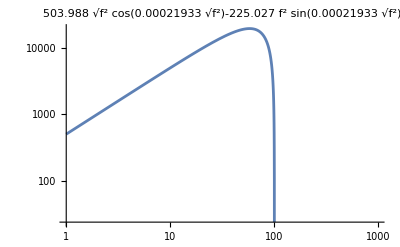

```mathematica
d1=s E0 k2 Cos[k2 L] - M ω^2 Sin[k2 L]/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4};
d1g=LogLogPlot[d1,{f,1,1000}(*,PlotRange->{10^-47,10^-37}*),PlotLabel->d1]
```

d2の実部と虚部（ただし k1= k’’(1-i)）

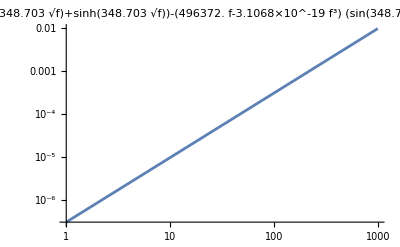

```mathematica
d2R=((α^2 T  ω^2)/Cv)/((ω/χ)^2+((ρ  ω^2)/(s E0))^2)(s E0  √(ω/(2χ))(2 (ρ  ω^2)/(s E0)(Sin[2 kd L] + Sinh[2kd L])-(ω/χ-χ/ω((ρ  ω^2)/(s E0))^2) (Sin[2kd L] - Sinh[2kd L]))/(Cosh[2kd L]-Cos[2kd L])-2 (ρ  ω^2)/(s E0) M  ω^2)/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
d2Rg=LogLogPlot[d2R,{f,1,1000}(*,PlotRange->{10^-47,10^-37}*),PlotLabel->d2R]
```

```mathematica
d2I=((α^2 T ω^2)/Cv)/((ω/χ)^2+((ρ ω^2)/(s E0))^2)(-s E0 √(ω/(2χ))(2 (ρ ω^2)/(s E0)(Sin[2kd L] - Sinh[2kd L])+(ω/χ-χ/ω((ρ ω^2)/(s E0))^2) (Sin[2kd L] + Sinh[2kd L]))/(Cosh[2kd L]-Cos[2kd L]))
```

d1とd2の実部の大きさの比較

```mathematica
Show[d1g,d2Rg]
```

-Graphics-